Some optimations which are not safe??
Only one up and one down particle taken for potential and kinetic energy and multiplied with 2 (as there are two up and two down which should be symmetrized)

```mathematica
LaunchKernels[]
```

{Local,Local,Local,Local}

```mathematica
ClearAll[ alpha1,alpha2,alpha3,alpha4]
aaa={ alpha1,alpha2,alpha3,alpha4};
(*Well positions*)
ClearAll[p1,p2,p3,p4];
wellPositions={p1,p2,p3,p4};
signWavefunctions={sn1,sn2,sn3,sn4};
(*Satial wavefunction*)
phiSpatial[x_,center_]:=signWavefunctions[[center]]*Exp[-aaa[[center]]*(x-wellPositions[[center]])^2];

(*Spin wavefunction*)
chiSpin[sigma_,spin_]:=KroneckerDelta[sigma,spin];

(*Combined spatial and spin basis*)
phi[x_,sigma_,center_,spin_]:=phiSpatial[x,center]*chiSpin[sigma,spin];
```

```mathematica
(*Generate all valid spin configurations*)
validSpinConfigurations=Permutations[{"up","up","down","down"}];
validSpinConfigurations={{"up","down","up","down"}};

(*Total wavefunction summed over all valid spin configurations*)
PsiTotal[x_,sigma_]:=Sum[Det[Table[phi[x[[i]],sigma[[i]],j,spinConfig[[j]]],{i,4},{j,4}]],{spinConfig,validSpinConfigurations}];
```

```mathematica
DoInt2[f_]:=(Integrate[f,{x3,-Infinity,Infinity},{x4,-Infinity,Infinity},Assumptions->alpha1>0 && alpha2>0 &&alpha3>0&&alpha4>0&& a>0])
```

```mathematica
DoInt3[f_]:=(Integrate[f,{x2,-Infinity,Infinity},{x3,-Infinity,Infinity},{x4,-Infinity,Infinity},Assumptions->alpha1>0 && alpha2>0&&alpha3>0&&alpha4>0&& a>0])
```

```mathematica
DoInt4[f_]:=(Integrate[Simplify[f],{x1,-Infinity,Infinity},{x2,-Infinity,Infinity},{x3,-Infinity,Infinity},{x4,-Infinity,Infinity},Assumptions-> alpha1>0 &&alpha2>0 &&alpha3>0&&alpha4>0 && a>0])
```

```mathematica
ClearAll[s1,s2,s3,s4,a,AmpPot]
```

```mathematica
V[x_]:=Sum[-Exp[-a (x-xi)^2],{xi,wellPositions}];
V[x_]:=-AmpPot*Cos[2*Pi*x*a];
```

```mathematica
a
```

a

```mathematica
KineticEnergy[{x1_,x2_,x3_,x4_},spins_]:=Simplify[-1/2*(D[PsiTotal[{x1,x2,x3,x4},spins],{x1,2}]+D[PsiTotal[{x1,x2,x3,x4},spins],{x2,2}]+D[PsiTotal[{x1,x2,x3,x4},spins],{x3,2}]+D[PsiTotal[{x1,x2,x3,x4},spins],{x4,2}])];
EnergyIntegrand[{x1_,x2_,x3_,x4_},spins_]:=PsiTotal[{x1,x2,x3,x4},spins]*(KineticEnergy[{x1,x2,x3,x4},spins]+(V[x1]+V[x2]+V[x3]+V[x4])*PsiTotal[{x1,x2,x3,x4},spins]);
```

```mathematica
(*TotalEnergy=ParallelMap[DoInt4,Expand[EnergyIntegrand[{x1,x2,x3,x4},{"up","down","up","down"}]],Method->"FinestGrained"];*)
```

```mathematica
InputList=List @@ Expand[EnergyIntegrand[{x1,x2,x3,x4},{"up","down","up","down"}]];
```

```mathematica
(*InputList = InputList[[1;;5]];*)
Length[InputList]
```

292

```mathematica
sublength=40;
TotalEnergySub[ppp_]:=(CloseKernels[];LaunchKernels[];ParallelEvaluate[$HistoryLength=10];ParallelMap[DoInt4,ppp, Method->"FinestGrained"]);
result = Map[TotalEnergySub,Partition[InputList,sublength,sublength,1,{}]];
```

```mathematica
result=Flatten[result];
```

```mathematica
Length[result]
```

292

```mathematica
TotalEnergy = Plus @@ result;
(*memory problems with longer runs in subkernels*)
```

```mathematica
CloseKernels[];LaunchKernels[];ParallelEvaluate[$HistoryLength=10];
```

```mathematica
Normalization = ParallelMap[DoInt4,Expand[PsiTotal[{x1,x2,x3,x4},{"up","down","up","down"}]^2],Method->"FinestGrained"];
```

```mathematica
CloseKernels[];LaunchKernels[];ParallelEvaluate[$HistoryLength=10];
```

```mathematica
summandCorrelation=ParallelMap[DoInt2,Expand[PsiTotal[{x1,x2,x3,x4},{"up","down",s3,s4}]^2],Method->"FinestGrained"];
```

```mathematica
CloseKernels[];LaunchKernels[];ParallelEvaluate[$HistoryLength=10];
```

```mathematica
TwoParticleCorrelationUpDownududn[xx1_,xx2_,al1_,al2_,al3_,al4_,aa_,pp1_,pp2_,pp3_,pp4_]:=Sum[summandCorrelation /.{x1->xx1,x2->xx2,s3->sigma34[[1]],s4->sigma34[[2]],alpha1->al1,alpha2->al2,alpha3->al3,alpha4->al4, a->aa,p1->pp1,p2->pp2,p3->pp3,p4->pp4},{sigma34,{{"up","down"}}}];
```

```mathematica
summandDensityU=ParallelMap[DoInt3,Expand[PsiTotal[{x1,x2,x3,x4},{"up",s2,s3,s4}]^2],Method->"FinestGrained"];
```

```mathematica
CloseKernels[];LaunchKernels[];ParallelEvaluate[$HistoryLength=10];
```

```mathematica
OneParticleDensityUududn[xx1_,al1_,al2_,al3_,al4_,aa_,pp1_,pp2_,pp3_,pp4_]:=Sum[summandDensityU/Normalization /.{x1->xx1,s2->sigma234[[1]],s3->sigma234[[2]],s4->sigma234[[3]],alpha1->al1,alpha2->al2,alpha3->al3,alpha4->al4, a->aa,p1->pp1,p2->pp2,p3->pp3,p4->pp4},{sigma234,{{"down","up","down"}}}];
```

```mathematica
CloseKernels[];LaunchKernels[];ParallelEvaluate[$HistoryLength=10];
```

```mathematica
summandDensityD=ParallelMap[DoInt3,Expand[PsiTotal[{x2,x1,x3,x4},{s2,"down",s3,s4}]^2],Method->"FinestGrained"];
```

```mathematica
OneParticleDensityDududn[xx1_,al1_,al2_,al3_,al4_,aa_,pp1_,pp2_,pp3_,pp4_]:=Sum[summandDensityD/Normalization /.{x1->xx1,s2->sigma234[[1]],s3->sigma234[[2]],s4->sigma234[[3]],alpha1->al1,alpha2->al2,alpha3->al3,alpha4->al4, a->aa,p1->pp1,p2->pp2,p3->pp3,p4->pp4},{sigma234,{{"up","up","down"}}}];
```

```mathematica
Energyududn[al1_,al2_,al3_,al4_,aa_,pp1_,pp2_,pp3_,pp4_]:=Evaluate[(TotalEnergy/Normalization)/.{alpha1->al1,alpha2->al2,alpha3->al3,alpha4->al4, a->aa,p1->pp1,p2->pp2,p3->pp3,p4->pp4}]
```

```mathematica
sn1=sn2=sn3=sn4=1;
```

```mathematica
Plot3D[TwoParticleCorrelationUpDownududn[x,y,0.3,0.3,0.3,0.3,0.3,-6,-2,6,2],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Plot3D[TwoParticleCorrelationUpDownududn[x,y,0.03,0.03,0.03,0.03,0.03,-6,-2,6,2],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

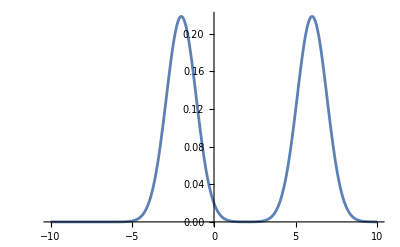

```mathematica
Plot[OneParticleDensityDududn[x,Sequence @@{0.3,0.3,0.3,0.3,0.3,-6,-2,2,6}],{x,-10,10}]
```

0.3

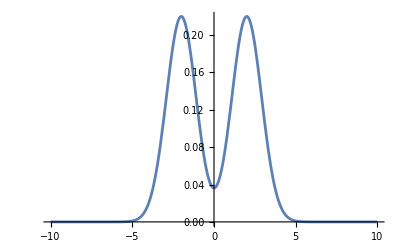

```mathematica
alpha1=alpha2 = alpha3=alpha4 =0.3
Plot[OneParticleDensityUududn[x,Sequence @@{0.3,0.3,0.3,0.3,0.3,-2,-2,2,6}],{x,-10,10}]
```

```mathematica
ClearAll[  alpha1,alpha2,alpha3,alpha4,a,p1,p2,p3,p4];
```

```mathematica
ClearAll[ alpha1,alpha2,alpha3,alpha4]
```

```mathematica
DoResults[parameters_,ww_]:= (
ppp={alpha1,alpha2,alpha3,alpha4, Sequence @@ parameters};
res=NMinimize[{Re[Energyududn[ alpha1,alpha2,alpha3,alpha4,Sequence @@ parameters]],alpha1>0 && alpha2>0 &&alpha3>0&&alpha4>0},{  alpha1,alpha2,alpha3,alpha4},Method->"DifferentialEvolution"];
ppp=ppp/.res[[2]];
Print[res];
ppp1=Plot[{0.2*V[x]/. Thread[{a,p1,p2,p3,p4}->parameters],OneParticleDensityUududn[x,Sequence @@ppp]+OneParticleDensityDududn[x,Sequence @@ppp],OneParticleDensityUududn[x,Sequence @@ppp],OneParticleDensityDududn[x,Sequence @@ppp]},{x,-ww,ww}, PlotStyle->{Black,Green, {Blue, Dashed},{Red,Dashed}},PlotLegends->{"0.25*V","Density","Density Up","Density Down"}, PlotRange->{Automatic,{-0.1,0.25}}]
)
```

Some tests systematically

```mathematica
pw=1/4
AmpPot=0.5
```

1/4

0.5

4 electrons seperated potentials, up electron plotted, Afterwords the energy per particle of the discussed particles is calculated

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

General::munfl: Exp[-5811.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5230.71] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5256.86] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

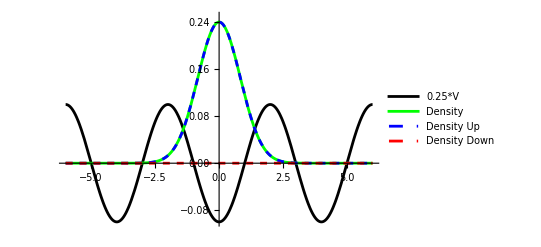

```mathematica
DoResults[{pw,0,-40,40,80},6]
```

```mathematica
eP=res[[1]]/4
```

-0.032281

Test with other positions

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

General::munfl: Exp[-778.762] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-732.266] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

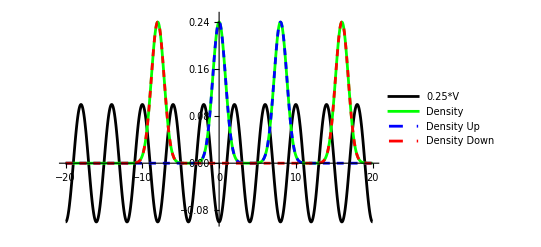

```mathematica
DoResults[{pw,0,-8,8,16},20]
```

```mathematica
res[[1]]-3*eP
```

-0.032281

Now two neighboring with oposite spin

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

General::munfl: Exp[-738.827] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

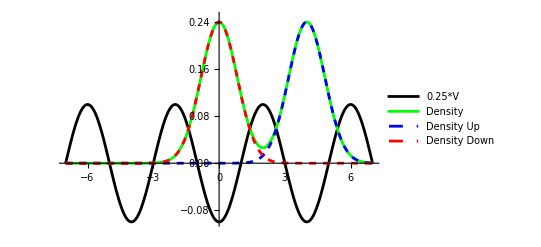

```mathematica
DoResults[{pw,-20,0,4,20},7]
```

```mathematica
(res[[1]]-2*eP)/2
```

-0.032281

Two neighboring with same spin

{-0.125508,{alpha1→0.372887,alpha2→0.363244,alpha3→0.372887,alpha4→0.363244}}

General::munfl: Exp[-712.167] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.568] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.167] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

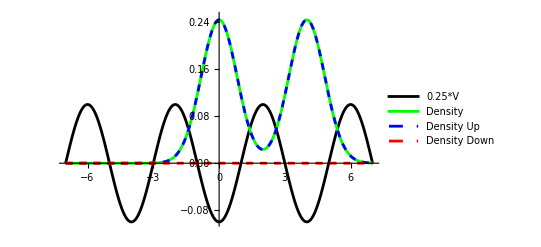

```mathematica
DoResults[{pw,-0,-20,4,20},7]
```

```mathematica
(res[[1]]-2*eP)/2
```

-0.030473

two pairs with oposite spin and an empty inbetween with opposite spin contact

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

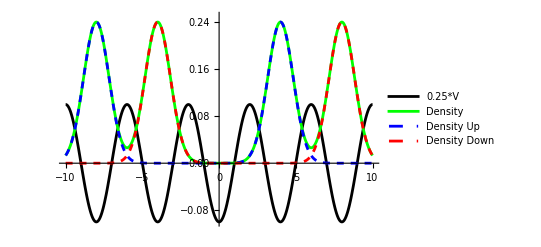

```mathematica
DoResults[{pw,-8,-4,4,8},10]
```

```mathematica
res[[1]]/4
```

-0.032281

same spin contact

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

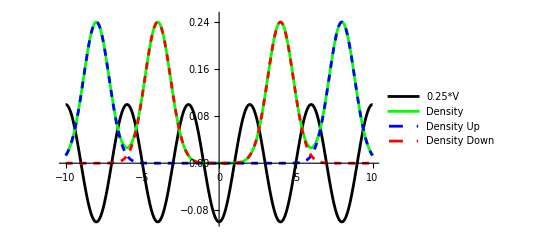

```mathematica
DoResults[{pw,-8,-4,8,4},10]
```

```mathematica
res[[1]]/4
```

-0.032281

two pairs with oposite spin and without empty inbetween with opposite spin contact

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

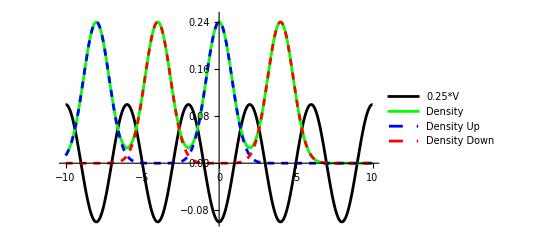

```mathematica
DoResults[{pw,-8,-4,0,4},10]
```

```mathematica
res[[1]]/4
```

-0.032281

two pairs with oposite spin and without empty inbetween with same spin contact

{-0.125508,{alpha1→0.363244,alpha2→0.372887,alpha3→0.363244,alpha4→0.372887}}

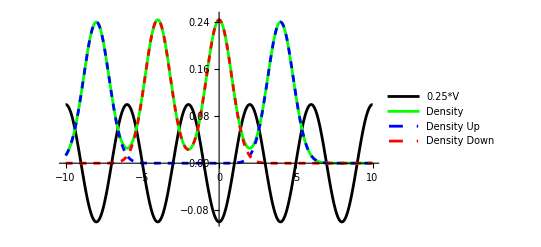

```mathematica
DoResults[{pw,-8,-4,4,0},10]
```

```mathematica
res[[1]]/4
```

-0.031377

two pairs with oposite spin and two empty inbetween with same spin contact

```mathematica
DoResults[{pw,-8,-4,8,4},10]
```

{-0.129124,{alpha1→0.363244,alpha2→0.363244,alpha3→0.363244,alpha4→0.363244}}

-Graphics-

```mathematica
res[[1]]/4
```

-0.032281

sn1 = sn2 = sn3 = sn4 = 1;
sn1 = sn3 = -1;
4 electrons seperated potentials, up electron plotted, Afterwords the energy per particle of the discussed particles is calculated
This gave the same results as above

```mathematica
sn1 = sn2 = sn3 = sn4 = 1;
```

```mathematica
DoResults[parameters_,ww_]:= (
ppp={alpha1,alpha2,alpha3,alpha4, Sequence @@ parameters};
res=NMinimize[{Re[Energyududn[ alpha1,alpha2,alpha3,alpha4,Sequence @@ parameters]],alpha1>0.1 && alpha2>0.1 &&alpha3>0.1&&alpha4>0.1},{  alpha1,alpha2,alpha3,alpha4},Method->"DifferentialEvolution"];
ppp=ppp/.res[[2]];
Print[res];
ppp1=Plot[{0.2*V[x]/. Thread[{a,p1,p2,p3,p4}->parameters],OneParticleDensityUududn[x,Sequence @@ppp]+OneParticleDensityDududn[x,Sequence @@ppp],OneParticleDensityUududn[x,Sequence @@ppp],OneParticleDensityDududn[x,Sequence @@ppp]},{x,-ww,ww}, PlotStyle->{Black,Green, {Blue, Dashed},{Red,Dashed}},PlotLegends->{"0.25*V","Density","Density Up","Density Down"}, PlotRange->{Automatic,{-0.2,0.5}}]
)
```

```mathematica
pw=1/2
AmpPot=1.7
```

1/2

1.7

{-0.0344137,{alpha1→1.25067,alpha2→1.25067,alpha3→1.25067,alpha4→1.25067}}

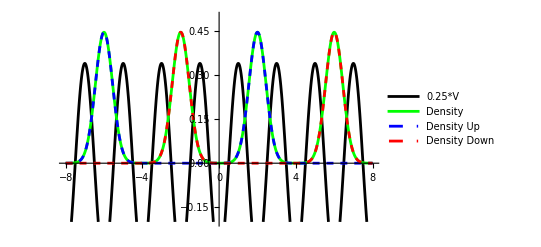

```mathematica
DoResults[{pw,-6,-2,2,6},8]
```

{-0.0344137,{alpha1→1.25067,alpha2→1.25067,alpha3→1.25067,alpha4→1.25067}}

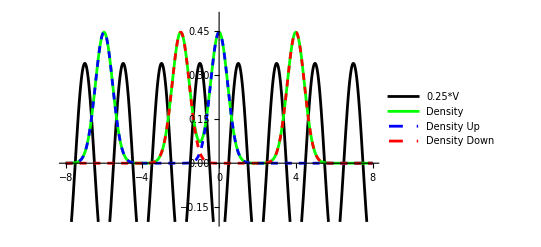

```mathematica
DoResults[{pw,-6,-2,0,4},8]
```

{-0.0105665,{alpha1→1.25067,alpha2→1.30719,alpha3→1.25067,alpha4→1.30719}}

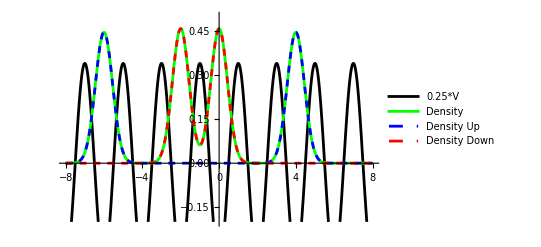

```mathematica
DoResults[{pw,-6,-2,4,0},8]
```

{-0.0344136,{alpha1→1.25067,alpha2→1.25067,alpha3→1.25067,alpha4→1.25067}}

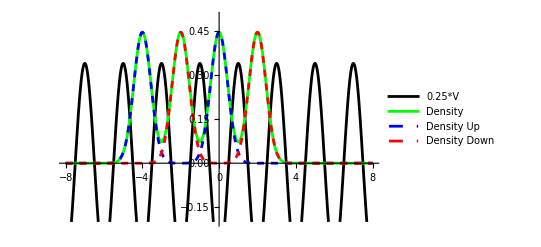

```mathematica
DoResults[{pw,-4,-2,0,2},8]
```

{0.0132807,{alpha1→1.30719,alpha2→1.30719,alpha3→1.30719,alpha4→1.30719}}

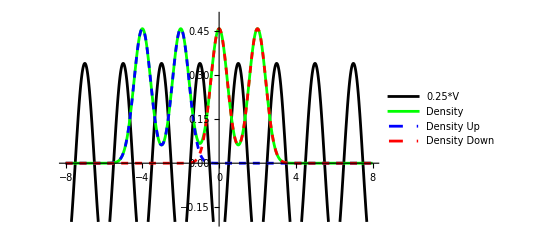

```mathematica
DoResults[{pw,-4,0,-2,2},8]
```

{-0.0105665,{alpha1→1.25067,alpha2→1.30719,alpha3→1.25067,alpha4→1.30719}}

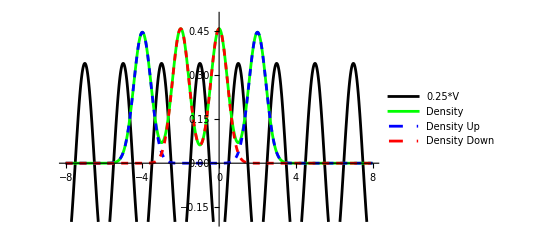

```mathematica
DoResults[{pw,-4,-2,2,0},8]
```